```mathematica
(*ClearAll["Global`*"]*)
```

```mathematica
<<"Loess.wl"
```

d26Mgsw data

```mathematica
data=d26Mgdata;
```

```mathematica
x=data[[All,1]];
y=data[[All,2]];
```

```mathematica
(*data=Transpose[{x,y}];*)
```

trend-line data from loess calculated using R-language

```mathematica
rloess=Drop[Import["/Users/philip/Repos/working/ps/data/interim/20180721pm-r19_loess-span.csv", {"Data",All,{1,2}}],1];
```

clean data : remove duplicates and switch the x axis to match model time scale

```mathematica
rloess=switch/@DeleteDuplicatesBy[rloess, First];
```

### add start and end values

```mathematica
yvmax=Part[rloess,1,2]; (* -0.83 *)
yvmax2=Part[loessdata0,1,2];
yvmin=-1.2;
```

```mathematica
rloess=Join[{{tmax,yvmax}},rloess,{{tmin,yvmin}}];(* add missing data points to convert rloess to valid co2 model input *)
```

loess model using `Loess.wl` compared with loess model calculated via script r19_loess.R

```mathematica
(*Dimensions[Range[0,15,.1]]*)
```

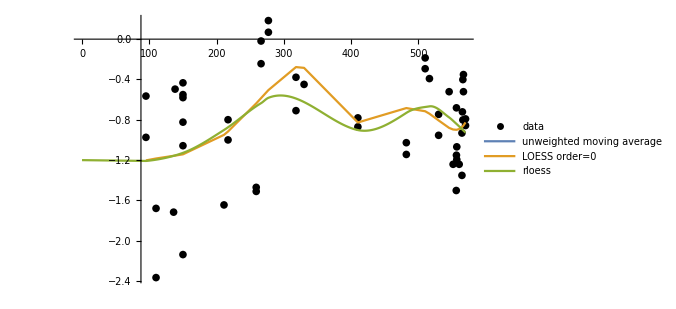

```mathematica
num=50;
loessfit0=Loess[data,num,6];
loessdata0=Transpose[{x,loessfit0/@x}];
loessdata01=Join[{{tmax,yvmax2}},loessdata0,{{tmin,yvmin}}];
movingaverage={x[[num/2;;-(num/2+1)]],MovingAverage[y,num]}ᵀ;
p4=ListPlot[data,PlotStyle->Black,PlotLegends->{"data"}];
p5=ListLinePlot[{movingaverage, loessdata0,rloess},PlotLegends->{"unweighted moving average","LOESS order=0", "rloess"}];
Show[{p4,p5},ImageSize->500, PlotRange->All]
```

```mathematica
loessMV[[All,2]]
```

{-1.2,-1.19467,-1.18611,-1.17656,-1.16449,-1.15622,-1.14795,-1.14501,-1.14248,-1.14248,-1.1038,-1.0585,-1.01319,-0.912173,-0.811152,-0.738306,-0.672087,-0.590006,-0.563643,-0.491583,-0.430025,-0.370039,-0.434225,-0.498411,-0.579733,-0.661054,-0.747098,-0.724831,-0.707429,-0.731936,-0.756442,-0.789494,-0.825708,-0.85763,-0.876173,-0.894715,-0.898335,-0.898794,-0.897238,-0.89191,-0.886582,-0.880443,-0.873327,-0.867652,-0.86443,-0.861209,-0.852897,-0.845562,-0.838226,-0.82626}

```mathematica
loessMV=Reverse[ Join[{{tmax,yvmax2}},MovingAverage[loessdata01,6],{{tmin,yvmin}}] ];
```

```mathematica
loessIF=ListInterpolation[loessMV[[All,2]],{{0,570}}]
```

InterpolatingFunction[…]

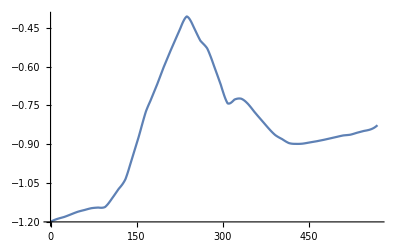

```mathematica
Plot[loessIF[t],{t,0,570}]
```

```mathematica
Veizer87
```

{{-0.04,0.7085},{-0.03,0.7085},{-0.02,0.7085},{-0.01,0.7085},{0,0.7085},{5.7415,0.708661},{46.0457,0.709126},{55.1711,0.709158},{77.2243,0.708945},{93.9544,0.708787},{99.2776,0.708654},{107.643,0.708362},{110.684,0.708181},{113.726,0.708032},{115.247,0.707953},{120.57,0.707882},{126.654,0.707811},{129.696,0.708024},{135.019,0.708205},{138.821,0.708394},{146.426,0.708559},{150.989,0.708685},{156.312,0.708764},{166.958,0.708756},{172.281,0.708575},{176.084,0.708386},{179.126,0.708142},{182.167,0.707976},{184.449,0.707882},{186.73,0.707795},{189.772,0.707929},{195.856,0.708087},{201.939,0.708283},{208.783,0.70826},{212.586,0.708087},{217.148,0.707929},{220.19,0.707819},{227.034,0.707669},{233.118,0.707882},{237.681,0.708079},{244.525,0.708213},{257.453,0.708276},{269.62,0.708244},{277.985,0.708118},{281.027,0.707953},{284.069,0.70778},{286.35,0.707646},{298.517,0.707535},{305,0.70753},{314.487,0.707024},{323.612,0.70715},{334.259,0.707575},{343.384,0.707661},{349.468,0.70778},{354.03,0.707787},{363.156,0.707764},{370.761,0.70752},{376.844,0.707268},{381.407,0.707095},{385.209,0.707228},{392.814,0.707291},{396.616,0.707283},{400.418,0.707228},{404.221,0.707047},{411.825,0.706811},{419.43,0.70715},{426.274,0.707268},{433.878,0.707402},{438.441,0.70748},{440.722,0.707417},{448.327,0.707394},{452.89,0.707268},{462.776,0.707339},{469.62,0.707425},{477.224,0.707409},{480.266,0.707315},{483.308,0.707433},{487.871,0.707543},{492.433,0.707646},{498.517,0.707772},{503.08,0.707819},{509.163,0.707803},{510.684,0.70774},{522.852,0.707756},{529.696,0.707764},{537.3,0.707937},{543.384,0.708158},{547.186,0.708409},{550.989,0.708701},{554.791,0.708882},{562.395,0.709008},{567.719,0.7091},{569.98,0.7091},{569.99,0.7091},{570.,0.7091},{570.01,0.7091},{570.02,0.7091}}

```mathematica
matheloess
```

Interpolation[{{0,-1},{82,-1},{109,-1},{118,-1},{129,-1},{137,-1},{145,-1},{148,-1},{150,-1},{150,-1},{162,-1},{176,-1},{189,-1},{211,-1},{233,-1},{244,-1},{253,-1},{265,-1},{269,-1},{281,0},{291,0},{304,0},{331,0},{357,0},{390,-1},{423,-1},{459,-1},{479,-1},{500,-1},{510,-1},{519,-1},{526,-1},{535,-1},{543,-1},{548,-1},{553,-1},{556,-1},{557,-1},{558,-1},{559,-1},{561,-1},{562,-1},{564,-1},{565,-1},{566,-1},{566,-1},{567,-1},{568,-1},{569,-1},{570,-1}},InterpolationOrder→1]

```mathematica
testt[t]
```

Interpolation[{{0,-1.2},{82.,-1.19467},{109.22,-1.18611},{117.88,-1.17656},{128.88,-1.16449},{136.88,-1.15622},{144.88,-1.14795},{147.66,-1.14501},{150.,-1.14248},{150.,-1.14248},{162.2,-1.1038},{175.6,-1.0585},{189.,-1.01319},{210.78,-0.912173},{232.56,-0.811152},{243.58,-0.738306},{253.4,-0.672087},{265.4,-0.590006},{269.02,-0.563643},{280.84,-0.491583},{291.22,-0.430025},{304.,-0.370039},{330.6,-0.434225},{357.2,-0.498411},{390.,-0.579733},{422.8,-0.661054},{458.8,-0.747098},{478.8,-0.724831},{500.07,-0.707429},{509.67,-0.731936},{519.27,-0.756442},{526.396,-0.789494},{534.705,-0.825708},{542.677,-0.85763},{547.976,-0.876173},{553.275,-0.894715},{555.549,-0.898335},{556.64,-0.898794},{557.513,-0.897238},{559.148,-0.89191},{560.783,-0.886582},{562.453,-0.880443},{564.261,-0.873327},{565.355,-0.867652},{565.802,-0.86443},{566.249,-0.861209},{567.177,-0.852897},{567.967,-0.845562},{568.759,-0.838226},{570,-0.82626}},InterpolationOrder→1][t]

```mathematica
lf101[t_]:=Interpolation[loessMV,InterpolationOrder->3][t]
```

-Graphics-

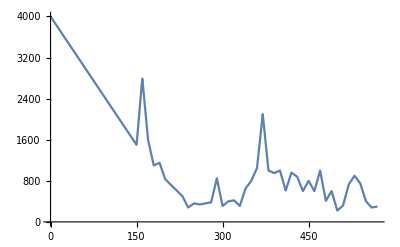

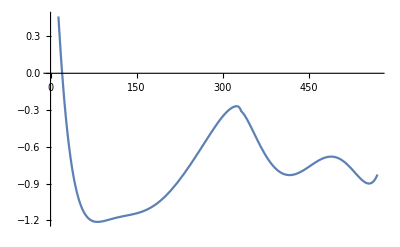

```mathematica
Plot[lf101[t],{t,tmin,tmax}]
Plot[pCO2data[t],{t,tmin,tmax}]
Plot[loessfit0[t],{t,0,570}]
```

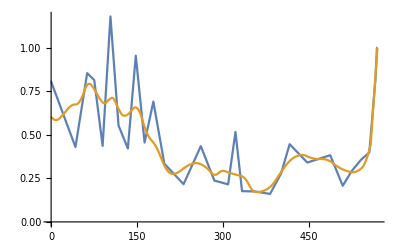

```mathematica
ListPlot[{fERint,fER}, Joined->True]
```

```mathematica
Table[{x,loessfit0[t]},{t,0,570}]
```

{{{569.992,569.992,566.906,566.906,566.04,566.04,565.354,564.67,564.67,560.573,557,557,556.495,556.495,556.211,551.545,545.63,530,530,516.35,510,510,482,482,410,410,330,318,318,277,277,266.1,266.1,258.9,258.9,217,217,211,150,150,150,150,150,150,138.3,136.1,110,110,95,95},1.91017},569,{{569.992,569.992,46,95,95},1}}
 |  |  |  |